## The spin plot

```mathematica
spin={{0,0,0},{0,1/3,1/6}};
b={{0,0,0},{0,0,1/2}};
v1={{0,0,0},{1/2,0,0}};
J={{0,0,0},{0,1/2,0}};
```

```mathematica
(*Define unit vectors of spin and J*)spinVec=Normalize[spin[[2]]];
jVec=Normalize[J[[2]]];

(*Create a rotation axis (perpendicular to the plane of spin and J)*)
normalVec=Normalize[Cross[spinVec,jVec]];

(*Arc points between spinVec and jVec*)
arc=Table[RotationTransform[θ,normalVec][spinVec]*0.08,(*0.2=arc radius*){θ,0,VectorAngle[spinVec,jVec],VectorAngle[spinVec,jVec]/20}];
```

## Plot the bending angle.

```mathematica
heavyParticle=Line[{{0,0},{5,0}}];
probe = Line[{{0,1},{5,1}}];
blackhole=Disk[{3,0},0.15];
```

```mathematica
trajecFun[x_]:=4/(x-3)
```

```mathematica
trajecFun[1.5Pi]
```

2.15664

```mathematica
p=1;
e=2;
r[t_]:=p/(1+e*Cos[t])
traj[t_]:={r[t]*Cos[t],r[t]*Sin[t]}
```

```mathematica
part1=Graphics[{
Thick,heavyParticle,
Dashed, probe,
Black,blackhole
}];
```

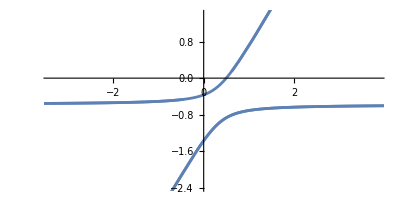

```mathematica
trajectory=ParametricPlot[rotmat[Pi/3].traj[t],{t,-5,5}]
```

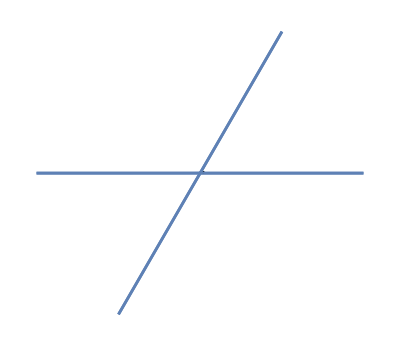

```mathematica
Show[part1,trajectory]
```

```mathematica
a=1.2;
b=2;
traj[t_]:={a*Cosh[t],b*Sinh[t]}
```

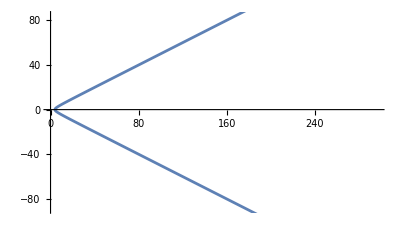

```mathematica
ParametricPlot[traj[t],{t,-5,5}]
```

```mathematica
Clear[rotmat]
rotmat[rot_]:={{Cos[rot],Sin[rot]},{-Sin[rot],Cos[rot]}};
```

```mathematica
newtraj[t_]:=rotmat[Pi/4].traj[t]
```

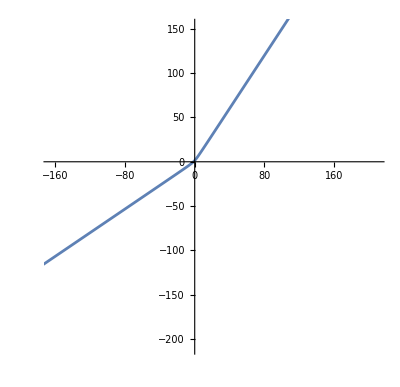

```mathematica
ParametricPlot[-newtraj[t],{t,-5,5}]
```

```mathematica
Clear[r,p,e]
```

```mathematica
r[t_]:=p/(1+e*Cos[t])
```

```mathematica
p=1;
e=2;
traj[t_]:={r[t]*Cos[t],r[t]*Sin[t]}
```

```mathematica
ParametricPlot[rotmat[Pi/3].traj[t],{t,-5,5}]
```

-Graphics-